```mathematica
Clear[θ];R[θ_]:={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};a=2.1;
```

```mathematica
f1[θ_]:=RegionPlot[-0.5<x<0.5 &&  -2<y<2 , {x,-a,a},{y,-a,a},PlotStyle->GrayLevel[0.5],Frame->False]
```

```mathematica
f2[θ_]:= RegionPlot[-0.5<x Cos[θ]-y Sin[θ]<0.5 &&  -2<y Cos[θ]+x Sin[θ]<2 , {x,-a,a},{y,-a,a},PlotStyle->GrayLevel[0.5],Frame->False]
```

```mathematica
f3[θ_]:=RegionPlot[-0.5<x<0.5 &&  -2<y<2  && -0.5<x Cos[θ]-y Sin[θ]<0.5 &&  -2<y Cos[θ]+x Sin[θ]θ<2 , {x,-a,a},{y,-a,a},PlotStyle->GrayLevel[0.5 Cos[θ]^2],Frame->False]
```

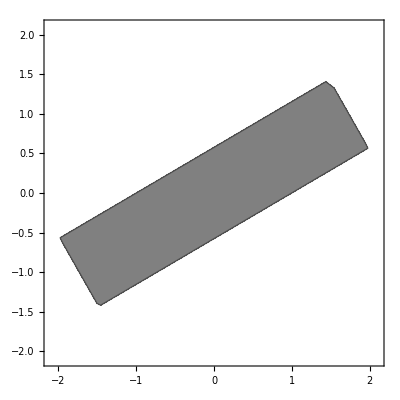

```mathematica
f2[π/3]
```

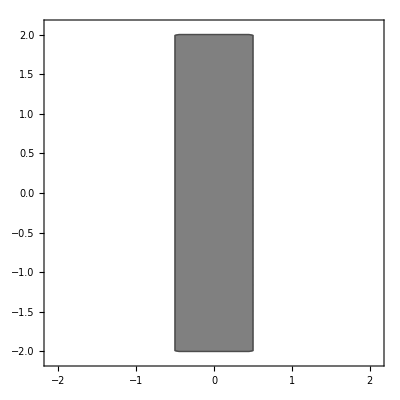
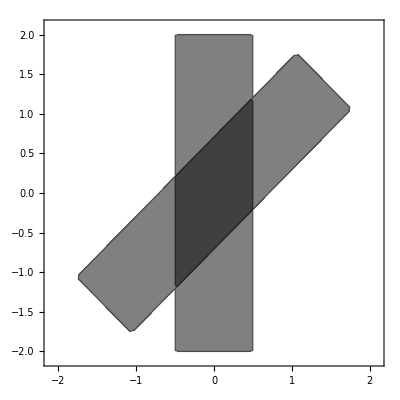
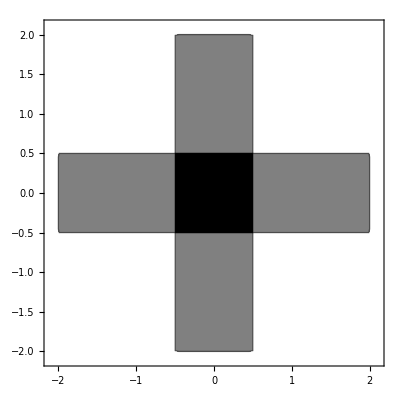
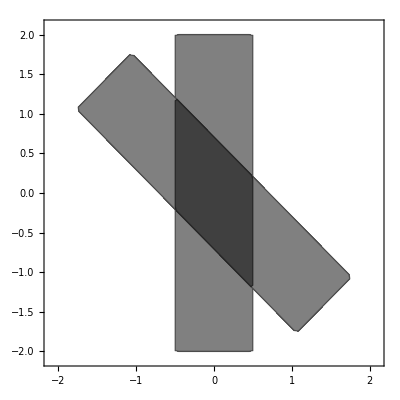
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{f1[θ],f2[θ],f3[θ]}],{θ,0,π,2π/8}]
```

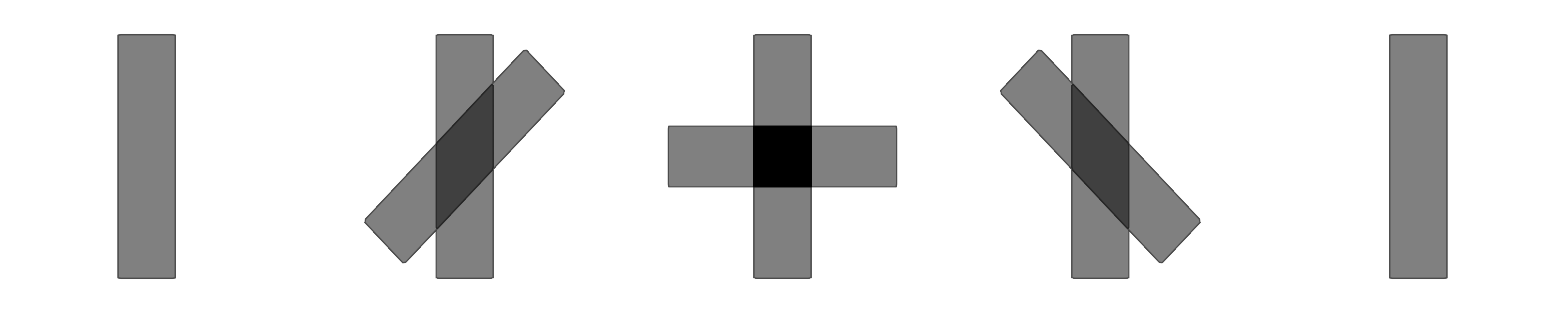

```mathematica
GraphicsGrid[{Table[Show[{f1[θ],f2[θ],f3[θ]}],{θ,0,π,2π/8}]},Frame->False]
```

```mathematica
Animate[Show[{f1[θ],f2[θ],f3[θ]}],{θ,0,2π}]
```

```mathematica
Animate[Show[f2[θ]],{θ,0,2π}]
```